# Rayleigh channel data fitting

This notebook performs data fitting for the Rayleigh channel model.

### Copyright notice

Copyright (C) 2012 Donagh Horgan.
Email: donaghh@rennes.ucc.ie.

This program is free software : you can redistribute it and/or modify
it under the terms of the GNU General Public License as published by
the Free Software Foundation, either version 3 of the License, or
(at your option) any later version.

This program is distributed in the hope that it will be useful,
but WITHOUT ANY WARRANTY; without even the implied warranty of
MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE. See 
COPYING for more details.

You should have received a copy of the GNU General Public License
along with this program. If not, see http://www.gnu.org/licenses.

### Version information

02/08/2012
1.0

### Changelog

Version 1.0: This version was used in the submitted version of the paper.

## Set up

Clear all symbol values and load function definitions:

```mathematica
ClearAll["Global`*"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<definitions.m
<<plots.m
```

## Variables

Here, we define the ranges of values to be used for each parameter.

```mathematica
channelType="Rayleigh";
precision=∞;
nRange={1,2,3,4,5,10,20,50};
snrdbRange=Range[0,-21,-1];
snrRange=10^(snrdbRange/10);
pf=0.1;
pd=0.9;
```

## Data fitting

Generate data and fit it to the model:

```mathematica
data=Flatten[Table[{n,γ,SampleComplexity[γ,pf,pd,n,ChannelType->channelType,DatabaseLookup->True]},{n,nRange},{γ,snrRange}],1];
```

```mathematica
model=(a ⅇ^(b/n)+γ(c+d/n^e)+f+g/n^h)SampleComplexity[γ,pf,pd,n,ChannelType->"AWGN"];
```

```mathematica
fit=FindFit[data,model,{a,b,c,d,{e,9},f,g,{h,9}},{n,γ},MaxIterations->10000]
```

{a→1.13257,b→2.89472,c→1.26362,d→1.07861,e→13660.7,f→-0.133695,g→2.66148,h→5.28098}

```mathematica
modelf=Function[{n,γ},Evaluate[model/.fit]];
```

Calculate various error metrics:

```mathematica
{x,y,z}=Transpose[data];
```

```mathematica
exact=z;
approx=Apply[modelf,{x,y}];
```

```mathematica
error=exact-approx;
absError=Abs[error];
relError=error/exact;
absRelError=Abs[relError];
```

## Results

### Error statistics

#### Error and absolute error

Probability density function of the approximation error:

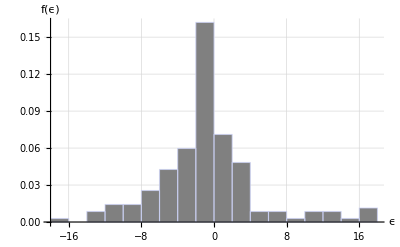

```mathematica
CustomHistogram[error,{"ϵ","f(ϵ)"}]
```

Histogram statistics:

```mathematica
StatsTable[error]
```

| μ | σ
 | -0.761611 | 5.55512

```mathematica
StatsTable[absError]
```

| μ | σ
 | 3.7374 | 4.1707

Largest errors:

```mathematica
MaxErrorsTable[absError,10]
```

γ (dB) | n | m | ϵ | ϵ_r
-17. | 2. | 1. | 17.4432 | 0.000221299
-21. | 2. | 1. | -17.3344 | -0.0000349749
-16. | 2. | 1. | 16.758 | 0.00033646
-18. | 2. | 1. | 16.4615 | 0.000131927
-21. | 5. | 1. | 16.0414 | 0.00020294
-15. | 2. | 1. | 15.2897 | 0.000485622
-14. | 2. | 1. | 13.5405 | 0.000680007
-18. | 4. | 1. | -13.353 | -0.000459459
-17. | 4. | 1. | -13.2273 | -0.00071985
-19. | 2. | 1. | 12.3024 | 0.0000622673

#### Relative error and absolute relative error

Probability density function of the relative approximation error:

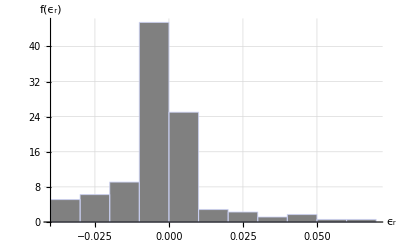

```mathematica
CustomHistogram[relError,{"ϵ_r","f(ϵ_r)"}]
```

Histogram statistics:

```mathematica
StatsTable[relError]
```

| μ | σ
 | -0.0026411 | 0.0149982

```mathematica
StatsTable[absRelError]
```

| μ | σ
 | 0.00899485 | 0.0122716

Largest relative errors:

```mathematica
MaxErrorsTable[absRelError,10]
```

γ (dB) | n | m | ϵ | ϵ_r
0. | 2. | 1. | 2.68833 | 0.0637095
0. | 3. | 1. | 1.06841 | 0.0560235
0. | 4. | 1. | 0.569796 | 0.0476491
-1. | 2. | 1. | 2.81383 | 0.0448603
0. | 5. | 1. | 0.35191 | 0.0407659
-4. | 50. | 1. | -0.0992433 | -0.039651
-5. | 50. | 1. | -0.141793 | -0.0382141
-3. | 50. | 1. | -0.0652879 | -0.0381169
-6. | 50. | 1. | -0.194994 | -0.0350196
-1. | 3. | 1. | 0.966745 | 0.0349074